-Graphics-

where is this pressure maximal?

p[a,θ]=p_∞+1/2 ρ U^2(1-9/4 Sin[θ]^2)

so a is constant!, we are interested in the angular position on the surface at which the pressure is maximal

∂/(∂θ)p[a,θ]=0

so at the peak of the local minimal the derivative is zero, i.e. the function is insensitive to changes, it is at the poling position

```mathematica
Clear[p];D[Subscript[p, ∞]+1/2 ρ U^2(1-9/4 Sin[θ]^2) ,θ]
```

-9/4 U^2 ρ Cos[θ] Sin[θ]

∂/(∂θ)p[a,θ]=-9/4 U^2 ρ Cos[θ] Sin[θ]=0

-9/4 U^2 ρ Cos[θ] Sin[θ]=0

Cos[θ] Sin[θ]=0

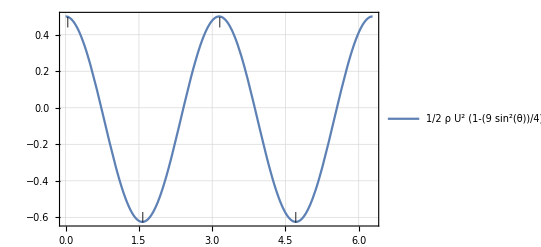

```mathematica
U=1;ρ=1;Plot[Labeled[1/2 ρ U^2(1-9/4 Sin[θ]^2),{"|","|","|","|"},{0,3.14/2,3.14,3.14+3.14/2}],{θ,0,2π},PlotTheme->"Detailed"]
```

so the maxima are at

```mathematica
Solve[Cos[θ] Sin[θ]==0&&0≤θ≤2π,θ]
```

{{θ→0},{θ→π/2},{θ→π},{θ→(3 π)/2},{θ→2 π}}

```mathematica
Clear[ρ,U];
{1/2 ρ U^2(1-9/4 Sin[θ]^2)/.{θ->π/2},1/2 ρ U^2(1-9/4 Sin[θ]^2)/.θ->0}
```

{-(5 U^2 ρ)/8,(U^2 ρ)/2}

p_max=p_∞+(U^2 ρ)/2

p_min=p_∞-(5 U^2 ρ)/8

the pressure maxima occur at the rear and forward stagnation points of the sphere

the pressure minima occur, where the velocity is fastest, above and below the sphere (where it would touch a top and bottom plate), this is the principle of the aeroplane wing (bernoulli principle?), it is interesting that in the invisid case the pressure is pushing equally from forward and backward, but in the viscous case, due to assymmetry in the wake there is a non-zero pressure difference and hence a net force!

-Graphics-

one can see that from the energy conservation law written as bernoulli's theorem, that we can see that when the pressure is high, the velocity is low and vice versa

## what is the critical stream speed U at which cavitation occurs?

Note that in the latter case (when p_min=p_∞-5/8 ρU^2, it is possible to have p_min=0

this happens only if

p_∞-5/8 ρU^2=0

p_∞-5/8 ρU^2=0

p_∞-5/8 ρU^2=0

```mathematica
Subscript[p, ∞]-5/8 ρU^2=0
```